```mathematica
NotebookDirectory[]
```

C:\Users\IBM_ADMIN\Box Sync\My Public Documents\Arnold's Cat\GitHub\Arnold-cat-lab\Mathematica\

```mathematica
Get["quad0mod4clas2.m", Path->NotebookDirectory[]];
QN = Drop[QN,-1];
For[k=1,k≤ Length@QN,k++,
QN[[k,2]]=Drop[QN[[k,2]],-1];
]
```

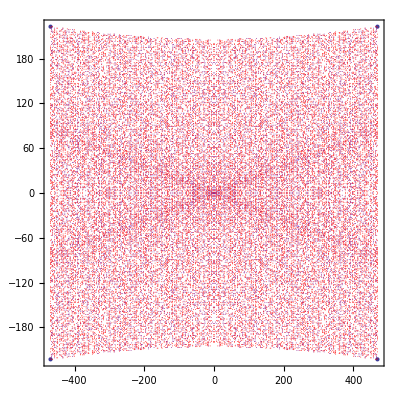
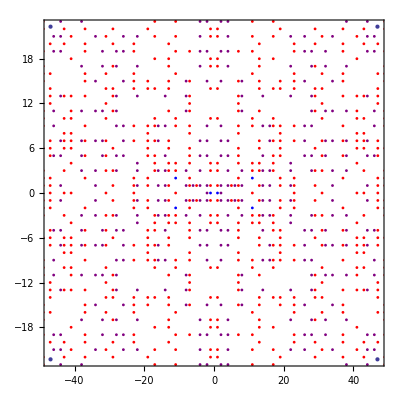
Δ = 30, β = 2, ξ = {0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, 1, 0, 0, 0, 1, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 0, 1, 0, -1, 0, 0, 0, 0, 0, 1, 0, 0, 0, -1, 0, -1, 0, 0, 0, -1, 0, 1, 0, 0, 0, -1, 0, 0, 0, 0, 0, -1, 0, -1, 0, 0, 0, 0, 0, -1, 0, 0, 0, 1, 0, -1, 0, 0, 0, -1, 0}
-Graphics-
-Graphics-

Δ = 26, β = 2, ξ = {0, 1, 0, -1, 0, 1, 0, -1, 0, 1, 0, 1, 0, 0, 0, -1, 0, 1, 0, 1, 0, 1, 0, 1, 0, 1, 0, -1, 0, -1, 0, -1, 0, -1, 0, -1, 0, 1, 0, 0, 0, -1, 0, -1, 0, 1, 0, -1, 0, 1, 0, -1, 0, -1, 0, 1, 0, -1, 0, 1, 0, -1, 0, -1, 0, 0, 0, 1, 0, -1, 0, -1, 0, -1, 0, -1, 0, -1, 0}
-Graphics-
-Graphics-

Δ = 15, β = 2, ξ = {0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 1, 0, -1, 0, 0, 0, 1, 0, -1, 0, 0, 0, -1, 0, 0, 0, 0, 0, -1, 0, -1, 0, 0, 0, 0, 0, -1, 0, 0, 0, -1, 0, 1, 0, 0, 0, -1, 0, 1, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1}
-Graphics-
-Graphics-

Δ = 10, β = 2, ξ = {0, 1, 0, 1, 0, 0, 0, -1, 0, 1, 0, -1, 0, 1, 0, 0, 0, -1, 0, -1, 0, -1, 0, -1, 0, 0, 0, 1, 0, -1, 0, 1, 0, -1, 0, 0, 0, 1, 0, 1}
-Graphics-
-Graphics-

```mathematica
Do[
Delta=QN[[k,1,2]];
If[Delta>0,
xmax=Max[#[[1,1]]&/@QN[[k,2]]]; 
ymax=Max[#[[1,2]]&/@QN[[k,2]]]; 
Print@Grid[{
{Text[StringForm["Δ = ``, β = ``, ξ = ``",QN[[k,1,2]],QN[[k,1,6]],Which[#=="o",0,#=="+",1,#=="-",-1]&/@Characters@QN[[k,1,8]]]]},
{Show[ListPlot[{{-xmax,-ymax},{-xmax,ymax},{xmax,-ymax},{xmax,ymax}},AspectRatio->1,Frame->True],(Graphics[{Which[#[[2]]=="p",Red,#[[2]]=="i",Purple,#[[2]]=="u",Blue],PointSize[0.0015],Point[{#[[1,1]],#[[1,2]]}]}])&/@QN[[k,2]],ImageSize->Full]},
{Show[ListPlot[{{-xmax/10,-ymax/10},{-xmax/10,ymax/10},{xmax/10,-ymax/10},{xmax/10,ymax/10}},AspectRatio->1,Frame->True],(Graphics[{Which[#[[2]]=="p",Red,#[[2]]=="i",Purple,#[[2]]=="u",Blue],PointSize[0.005],Point[{#[[1,1]],#[[1,2]]}]}])&/@QN[[k,2]],ImageSize->Full]}
}]
],
{k,Length@QN}]//Parallelize
```